```mathematica
m[t_]=a ⅇ^(-λ t)+a(1-ⅇ^(-λ t));
```

```mathematica
Needs["MultivariateStatistics`"]
PDF[MultinormalDistribution[{μx1+σ13/σ33(z-μx3),μx2+σ23/σ33(z-μx3)},{{σ11-(σ13)^2/σ33,σ12-(σ13 σ23)/σ33},{σ12-(σ13 σ23)/σ33,σ22-(σ23)^2/σ33}}],{x,y}]
```

ⅇ^(1/2 (-(((y-μx2-((z-μx3) σ23)/σ33) (-σ12+(σ13 σ23)/σ33))/(-σ12^2+σ11 σ22-(σ13^2 σ22)/σ33+(2 σ12 σ13 σ23)/σ33-(σ11 σ23^2)/σ33)+((x-μx1-((z-μx3) σ13)/σ33) (σ22-σ23^2/σ33))/(-σ12^2+σ11 σ22-(σ13^2 σ22)/σ33+(2 σ12 σ13 σ23)/σ33-(σ11 σ23^2)/σ33)) (x-μx1-((z-μx3) σ13)/σ33)-(((σ11-σ13^2/σ33) (y-μx2-((z-μx3) σ23)/σ33))/(-σ12^2+σ11 σ22-(σ13^2 σ22)/σ33+(2 σ12 σ13 σ23)/σ33-(σ11 σ23^2)/σ33)+((x-μx1-((z-μx3) σ13)/σ33) (-σ12+(σ13 σ23)/σ33))/(-σ12^2+σ11 σ22-(σ13^2 σ22)/σ33+(2 σ12 σ13 σ23)/σ33-(σ11 σ23^2)/σ33)) (y-μx2-((z-μx3) σ23)/σ33)))/(2 π √(-σ12^2+σ11 σ22-(σ13^2 σ22)/σ33+(2 σ12 σ13 σ23)/σ33-(σ11 σ23^2)/σ33))

```mathematica
expon[x_,y_]=1/2 (-(((y-μx2-((z-μx3) σ23)/σ33) (-σ12+(σ13 σ23)/σ33))/(-σ12^2+σ11 σ22-(σ13^2 σ22)/σ33+(2 σ12 σ13 σ23)/σ33-(σ11 σ23^2)/σ33)+((x-μx1-((z-μx3) σ13)/σ33) (σ22-σ23^2/σ33))/(-σ12^2+σ11 σ22-(σ13^2 σ22)/σ33+(2 σ12 σ13 σ23)/σ33-(σ11 σ23^2)/σ33)) (x-μx1-((z-μx3) σ13)/σ33)-(((σ11-σ13^2/σ33) (y-μx2-((z-μx3) σ23)/σ33))/(-σ12^2+σ11 σ22-(σ13^2 σ22)/σ33+(2 σ12 σ13 σ23)/σ33-(σ11 σ23^2)/σ33)+((x-μx1-((z-μx3) σ13)/σ33) (-σ12+(σ13 σ23)/σ33))/(-σ12^2+σ11 σ22-(σ13^2 σ22)/σ33+(2 σ12 σ13 σ23)/σ33-(σ11 σ23^2)/σ33)) (y-μx2-((z-μx3) σ23)/σ33))-2q σ x +((κ-λ)y^2)/2; (*!!!!!!!!!!!!!!!!!!!!!!!!!!*)
G=FullSimplify[expon[0,0]];
F=FullSimplify[Coefficient[expon[x,y], x y]];
A = -FullSimplify[Coefficient[expon[x,0], x^2]];
B=FullSimplify[Coefficient[expon[0,y], y^2]];
Cx=FullSimplify[Coefficient[expon[x,0],x]];
Dy=FullSimplify[Coefficient[expon[0,y],y]];
JYt=FullSimplify[Coefficient[(B (Cx)^2-Dy(A Dy + Cx F))/(4 *(A B)+F^2)+G,z]];
HYt2=FullSimplify[Coefficient[(B (Cx)^2-Dy(A Dy + Cx F))/(4 *(A B)+F^2)+G,z^2]];
constZ[z_]=(B (Cx)^2-Dy(A Dy + Cx F))/(4 *(A B)+F^2)+G;
L=FullSimplify[constZ[0]];
```

```mathematica
(*Check that the coefficients H,J and L are correct*)
FullSimplify[(B (Cx)^2-Dy(A Dy + Cx F))/(4 *(A B)+F^2)+G-HYt2*z^2-JYt*z-L]
```

0

```mathematica
(*Check that the coefficients A,B,C,D,F and G are correct*)
FullSimplify[expon[x,y]-((Cx *x)+(Dy *y)+(F* (x y))+(-A *x^2)+(B *y^2)+G)]
```

0

```mathematica
(* constant C_* in latex document*)
OC1 = FullSimplify[(2π)/(√A √(-(4 A B + F^2)/A))/(2 π √(-σ12^2+σ11 σ22-(σ13^2 σ22)/σ33+(2 σ12 σ13 σ23)/σ33-(σ11 σ23^2)/σ33))];
```

```mathematica
(* ---------------------------------
Now the outer integral

----------------------------
*)
PDF[MultinormalDistribution[{μa,μb},{{σaa,σab},{σab,σbb}}],{x,y}]
```

(ⅇ^(1/2 (-(y-μb) (((y-μb) σaa)/(-σab^2+σaa σbb)-((x-μa) σab)/(-σab^2+σaa σbb))-(x-μa) (-((y-μb) σab)/(-σab^2+σaa σbb)+((x-μa) σbb)/(-σab^2+σaa σbb)))))/(2 π √(-σab^2+σaa σbb))

```mathematica
expon1[x_,y_]=1/2 (-(y-μb) (((y-μb) σaa)/(-σab^2+σaa σbb)-((x-μa) σab)/(-σab^2+σaa σbb))-(x-μa) (-((y-μb) σab)/(-σab^2+σaa σbb)+((x-μa) σbb)/(-σab^2+σaa σbb)))+(c1) x+(c2)x^2+(c3)y;
G1=FullSimplify[expon1[0,0]];
F1=FullSimplify[Coefficient[expon1[x,y], x y]];
A1 = -FullSimplify[Coefficient[expon1[x,0], x^2]];
B1=FullSimplify[Coefficient[expon1[0,y], y^2]];
Cx1=FullSimplify[Coefficient[expon1[x,0],x]];
Dy1=FullSimplify[Coefficient[expon1[0,y],y]];
(*Check that the coefficients A1,B1,C1,D1,F1 and G1 are correct*)
FullSimplify[expon1[x,y]-((Cx1 *x)+(Dy1 *y)+(F1* (x y))+(-A1 *x^2)+(B1 *y^2)+G1)]
```

0

```mathematica
OC2=FullSimplify[(2π)/(√A1 √(-(4 A1 B1 + F1^2)/A1))/(2 π √(-σab^2+σaa σbb))];
```

```mathematica
(*Now need to collect coefficients for the triple integral*)
exponTrip[u_,v_,w_]=1/2 (-w ((w (-σab^2+σaa σbb))/(-σac^2 σbb+2 σab σac σbc-σaa σbc^2-σab^2 σcc+σaa σbb σcc)+(v (σab σac-σaa σbc))/(-σac^2 σbb+2 σab σac σbc-σaa σbc^2-σab^2 σcc+σaa σbb σcc)+(u (-σac σbb+σab σbc))/(-σac^2 σbb+2 σab σac σbc-σaa σbc^2-σab^2 σcc+σaa σbb σcc))-v ((w (σab σac-σaa σbc))/(-σac^2 σbb+2 σab σac σbc-σaa σbc^2-σab^2 σcc+σaa σbb σcc)+(v (-σac^2+σaa σcc))/(-σac^2 σbb+2 σab σac σbc-σaa σbc^2-σab^2 σcc+σaa σbb σcc)+(u (σac σbc-σab σcc))/(-σac^2 σbb+2 σab σac σbc-σaa σbc^2-σab^2 σcc+σaa σbb σcc))-u ((w (-σac σbb+σab σbc))/(-σac^2 σbb+2 σab σac σbc-σaa σbc^2-σab^2 σcc+σaa σbb σcc)+(v (σac σbc-σab σcc))/(-σac^2 σbb+2 σab σac σbc-σaa σbc^2-σab^2 σcc+σaa σbb σcc)+(u (-σbc^2+σbb σcc))/(-σac^2 σbb+2 σab σac σbc-σaa σbc^2-σab^2 σcc+σaa σbb σcc)))+(-2σ m[t] z +J)u +(-z σ^2+H)u^2-2q σ v +(-2σ  m[s] r)w + (-r σ^2)w^2;
C00=FullSimplify[exponTrip[0,0,0]];
Cu2=-Coefficient[exponTrip[u,0,0],u^2];
Cv2=Coefficient[exponTrip[0,v,0],v^2];
Cw2=Coefficient[exponTrip[0,0,w],w^2];
Cu=Coefficient[exponTrip[u,0,0],u];
Cv=Coefficient[exponTrip[0,v,0],v];
Cw=Coefficient[exponTrip[0,0,w],w];
Cuv=Coefficient[exponTrip[u,v,0],u v];
Cuw=Coefficient[exponTrip[u,0,w],u w];
Cvw=Coefficient[exponTrip[0,v,w],v w];
FullSimplify[exponTrip[u,v,w]-(-Cu2*u^2+Cv2*v^2+Cw2*w^2+Cu*u+Cv*v+Cw*w+Cuv*(u*v)+Cuw*(u*w)+Cvw*(v*w)+C00)]
```

0

```mathematica
κ=√(λ^2+2 q σ^2);
J=JYt;
H=HYt2;
c1=-2 z m[t] σ + J; (*!!!!!!!!!!!!!!!!!!!!!*)
c2=-z σ^2+H;
c3=-2 q σ;
gamma[z_,q_]=OC1*OC2*Exp[L]*Exp[(B1 (Cx1)^2-Dy1(A1 Dy1 + Cx1  F1))/(4 *(A1 B1)+F1^2)+G1];

(* Now to compute all the covariances*)
σ22=1/(2 κ)(1-ⅇ^(-2 κ T));
σ33=1/(2 κ)(1-ⅇ^(-2 κ t));
σ12=∫_t^T m[s](1/(2 κ)ⅇ^(-κ(s+T))(ⅇ^(2 κ s)-1))ⅆs;
σ13=∫_t^T m[s](1/(2 κ)ⅇ^(-κ(s+t))(ⅇ^(2 κ t)-1))ⅆs;
σ23=1/(2 κ)(ⅇ^(κ(t-T))-ⅇ^(-κ(t+T)));
σaa=1/(2 κ)(1-ⅇ^(-2 κ t));
σab=∫_0^t m[s](1/(2 κ)ⅇ^(-κ(s+t))(ⅇ^(2 κ s)-1))ⅆs;
```

```mathematica
(* σ11 and σbb precomputed in covariances.nb *)
σ11=-(a^2 (2+ⅇ^(-2 t κ)-2 ⅇ^((t-T) κ)+ⅇ^(-2 T κ)-2 ⅇ^(-(t+T) κ)+2 t κ-2 T κ))/(2 κ^3);
σbb=(a^2 ⅇ^(-2 t κ) (-1+4 ⅇ^(t κ)+ⅇ^(2 t κ) (-3+2 t κ)))/(2 κ^3);
(* We also need a few more covariances for second moment*)
σcc=1/(2 κ)(1-ⅇ^(-2 κ s));
σac=1/(2 κ)ⅇ^(-κ(s+t))(ⅇ^(2 κ s)-1);(* s ≤ t*)
σbc=-(a ⅇ^(-(s+t) κ) (-1+ⅇ^(s κ)) (1+ⅇ^(s κ)-2 ⅇ^(t κ)))/(2 κ^2);
```

```mathematica
(*Compute first moment*)
S0=110;
σ=5;

λ=2;
b=0;
a=22;
(*x=195; *)
μ=0.1;
σGBM=0.15;
μx1=0;
μx2=0;
μx3=0;
μa=0;
μb=0;
```

```mathematica
Clear[muPoints,sigmaPoints,xPoints,muTilde,sigmaTilde]
TEnd=1;
incrementSize=0.01;
i=1;
Do[
Phi[z_,q_]=Exp[-z (m[t])^2-q ∫_0^T (m[s])^2 ⅆs + ((λ-κ)T)/2-z*b-q *b*T]*gamma[z,q];
dzPhi[q_,t_]= Derivative[1,0][Phi][z,q] /.z-> 0;

moment1=NIntegrate[-S0 ⅇ^(μ t)dzPhi[q,t],{q,0,∞},{t,0,T}];
(* 
Now to set up the second moment
*)

OC2trip=1/(√Cu2 √(-(Cuv^2+4 Cu2 Cv2)/Cu2))2 π/(√((-Cuw^2 Cv2+Cuv Cuw Cvw+Cu2 Cvw^2-Cuv^2 Cw2-4 Cu2 Cv2 Cw2)/(Cuv^2 π+4 Cu2 Cv2 π)))/(2 √2 π^(3/2) √(-σac^2 σbb+2 σab σac σbc-σaa σbc^2-σab^2 σcc+σaa σbb σcc));
gamma2[z_,r_,q_]=OC1*OC2trip*Exp[L]*Exp[-(Cuw^2 (Cv^2-4 C00 Cv2)+4 C00 Cu2 Cvw^2-4 Cu2 Cv Cvw Cw+Cuv^2 Cw^2+4 Cu2 Cv2 Cw^2+Cuw (4 C00 Cuv Cvw-2 Cu Cv Cvw-2 Cuv Cv Cw+4 Cu Cv2 Cw)-4 C00 Cuv^2 Cw2+4 Cu2 Cv^2 Cw2-16 C00 Cu2 Cv2 Cw2+Cu Cuv (-2 Cvw Cw+4 Cv Cw2)+Cu^2 (Cvw^2-4 Cv2 Cw2))/(4 (Cuw^2 Cv2-Cuv Cuw Cvw-Cu2 Cvw^2+Cuv^2 Cw2+4 Cu2 Cv2 Cw2))];
Phi2[z_,r_,q_]=Exp[-z (m[t])^2-r (m[s])^2-q ∫_0^T (m[s])^2 ⅆs + ((λ-κ)T)/2]*gamma2[z,r,q];
dzdrPhi2[q_,t_,s_]=((Derivative[1,1,0][Phi2][z,r,q] /.z-> 0) /. r -> 0);
moment2=NIntegrate[S0^2 q Exp[μ(s+t)+σGBM^2 s]dzdrPhi2[q,t,s],{q,0,∞},{t,0,T},{s,0,t} ]+ NIntegrate[S0^2 q Exp[μ(s+t)+σGBM^2 t]dzdrPhi2[q,s,t],{q,0,∞},{t,0,T},{s,t,T} ];
muTilde[i]=Log[moment1/S0]/T;
sigmaTilde[i]=Sqrt[Log[((moment2-moment1^2)+(moment1)^2)/(moment1)^2]/T];
i++,
{T,incrementSize,TEnd,incrementSize}] (* END DO-LOOP*)
```

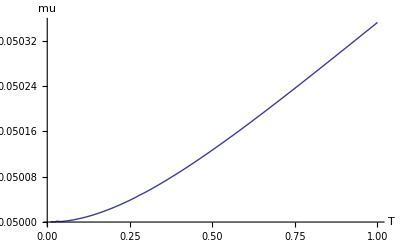

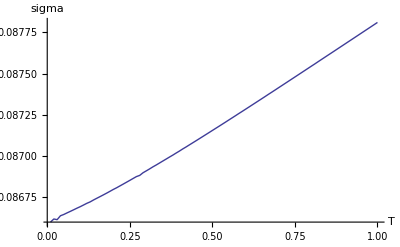

```mathematica
(* Plot graphs*)
xPoints=Table[T,{T,incrementSize,TEnd,incrementSize}];
muPoints=Table[{xPoints[[i]], muTilde[i]},{i,1,Length[xPoints]}]; 
sigmaPoints=Table[{xPoints[[i]], sigmaTilde[i]},{i,1,Length[xPoints]}];
ListLinePlot[muPoints,PlotRange->Full, AxesLabel->{Style[T,Large],Style["mu", Large]} ]
ListLinePlot[sigmaPoints,PlotRange->Full, AxesLabel->{Style[T,Large],Style["sigma", Large]} ]
```

```mathematica
muTilde[100]-muTilde[1]
sigmaTilde[100]-sigmaTilde[1]
```

0.000351263

0.00121038

```mathematica
?muTilde
```

Global`muTilde

muTilde[1]=0.0500008
 
muTilde[2]=0.0500001
 
muTilde[3]=0.0500015
 
muTilde[4]=0.0500008
 
muTilde[5]=0.0500014
 
muTilde[6]=0.0500021
 
muTilde[7]=0.050003
 
muTilde[8]=0.050004
 
muTilde[9]=0.0500051
 
muTilde[10]=0.0500064
 
muTilde[11]=0.0500078
 
muTilde[12]=0.0500093
 
muTilde[13]=0.0500109
 
muTilde[14]=0.0500127
 
muTilde[15]=0.0500145
 
muTilde[16]=0.0500165
 
muTilde[17]=0.0500186
 
muTilde[18]=0.0500208
 
muTilde[19]=0.050023
 
muTilde[20]=0.0500253
 
muTilde[21]=0.0500279
 
muTilde[22]=0.0500304
 
muTilde[23]=0.050033
 
muTilde[24]=0.0500357
 
muTilde[25]=0.0500384
 
muTilde[26]=0.0500413
 
muTilde[27]=0.0500442
 
muTilde[28]=0.0500476
 
muTilde[29]=0.0500503
 
muTilde[30]=0.0500534
 
muTilde[31]=0.0500566
 
muTilde[32]=0.0500599
 
muTilde[33]=0.0500632
 
muTilde[34]=0.0500666
 
muTilde[35]=0.05007
 
muTilde[36]=0.0500735
 
muTilde[37]=0.050077
 
muTilde[38]=0.0500806
 
muTilde[39]=0.0500843
 
muTilde[40]=0.0500879
 
muTilde[41]=0.0500916
 
muTilde[42]=0.0500954
 
muTilde[43]=0.0500992
 
muTilde[44]=0.0501031
 
muTilde[45]=0.050107
 
muTilde[46]=0.0501109
 
muTilde[47]=0.0501149
 
muTilde[48]=0.0501189
 
muTilde[49]=0.0501229
 
muTilde[50]=0.050127
 
muTilde[51]=0.0501311
 
muTilde[52]=0.0501352
 
muTilde[53]=0.0501393
 
muTilde[54]=0.0501435
 
muTilde[55]=0.0501477
 
muTilde[56]=0.050152
 
muTilde[57]=0.0501562
 
muTilde[58]=0.0501605
 
muTilde[59]=0.0501648
 
muTilde[60]=0.0501691
 
muTilde[61]=0.0501735
 
muTilde[62]=0.0501778
 
muTilde[63]=0.0501822
 
muTilde[64]=0.0501866
 
muTilde[65]=0.050191
 
muTilde[66]=0.0501955
 
muTilde[67]=0.0501999
 
muTilde[68]=0.0502044
 
muTilde[69]=0.0502089
 
muTilde[70]=0.0502133
 
muTilde[71]=0.0502179
 
muTilde[72]=0.0502224
 
muTilde[73]=0.0502269
 
muTilde[74]=0.0502314
 
muTilde[75]=0.050236
 
muTilde[76]=0.0502406
 
muTilde[77]=0.0502451
 
muTilde[78]=0.0502497
 
muTilde[79]=0.0502543
 
muTilde[80]=0.0502589
 
muTilde[81]=0.0502635
 
muTilde[82]=0.0502681
 
muTilde[83]=0.0502728
 
muTilde[84]=0.0502774
 
muTilde[85]=0.050282
 
muTilde[86]=0.0502867
 
muTilde[87]=0.0502913
 
muTilde[88]=0.050296
 
muTilde[89]=0.0503006
 
muTilde[90]=0.0503053
 
muTilde[91]=0.05031
 
muTilde[92]=0.0503146
 
muTilde[93]=0.0503193
 
muTilde[94]=0.050324
 
muTilde[95]=0.0503287
 
muTilde[96]=0.0503333
 
muTilde[97]=0.050338
 
muTilde[98]=0.0503427
 
muTilde[99]=0.0503474
 
muTilde[100]=0.0503521

```mathematica
(*
Print["First moment = " <> ToString[moment1]]
Print["Second moment = " <> ToString[moment2]]
Print["Variance = " <> ToString[moment2-moment1^2]]
Print["SD = " <> ToString[Sqrt[moment2-moment1^2]]]
Print["mu  tilde = " <> ToString[Log[moment1/S0]/T]]
Print["sig tilde = " <> ToString[Sqrt[Log[((moment2-moment1^2)+(moment1)^2)/(moment1)^2]/T]]]
*)
```